### 0.Notation

We will use Ψ[u]=:u*ψ[u], A0[u], Ax[u] to denote the scalar field and components of A.
τ=(4π)/3 T with T = the hawking temperature of the black hole

### 1. EOM

To simplify the eqn, we use our freedom to set τ =1 (And therefore we cannot set μ = chemical potential = c0 = 1 anymore because τ/μ is a dimensionless parameter of our theory)

```mathematica
h[u_]=1-u^3;
τ=1;
ϵ=1/1000;
```

The eom for A0 is :（Ref: eqn (14.43）in ads/cft duality user guide)

```mathematica
eomA0= A0''[u]-2/h[u]*ψ[u]^2*A0[u]
```

-(2 A0[u] ψ[u]^2)/(1-u^3)+A0''[u]

The eom for ψ[u] is: (Ref: eqn(14.44))

```mathematica
eompsi = u^2/h[u]*D[h[u]/u^2*D[u*ψ[u],u],u]+((A0[u]/(τ*h[u]))^2+2/(h[u]*u^2))*u*ψ[u] //Simplify
```

(u ((-u+u^4+A0[u]^2) ψ[u]+(-1+u^3) (3 u^2 ψ'[u]+(-1+u^3) ψ''[u])))/((-1+u^3)^2)

### 2. Shooting Method

#### 2.1 Series Expansion around the horizon u=1:

We expand A0[u] and ψ[u] around u=1: 
( Boundary Condition: A0 vanishes at the horizon to keep A^M A_M finite)

```mathematica
A0hor[u_]=a1(u-1)+a2(u-1)^2+a3(u-1)^3+a4(u-1)^4;
```

```mathematica
ψhor[u_]=b0+b1(u-1)+b2(u-1)^2+b3(u-1)^3+b4(u-1)^4;
```

Then, we plug the series expansion into the eoms to express all {a,b} in terms of a1 and b0:

```mathematica
eomhor = Series[{eomA0,eompsi}/.{A0->A0hor,ψ->ψhor},{u,1,3}] //Simplify;
```

For eomA0, we need the terms with power = {0,1,2}. For eompsi, we need{-1,0,1,2} (Because the existence of b0) . These 7 eqns help us express all {a,b} in terms of (a1,b0)

```mathematica
eomhorres= Solve[Join[Table[SeriesCoefficient[eomhor[[1]],n]==0,{n,0,2}],
Table[SeriesCoefficient[eomhor[[2]],n]==0,{n,-1,2}]],{a2,a3,a4,b1,b2,b3,b4}][[1]]
```

{a2→-(a1 b0^2)/3,a3→1/27 a1 (5 b0^2+b0^4),a4→1/972 a1 b0^2 (-90+3 a1^2-40 b0^2-2 b0^4),b1→-b0/3,b2→1/36 (4 b0-a1^2 b0),b3→1/972 b0 (-28+35 a1^2+8 a1^2 b0^2),b4→-(b0 (-64+1412 a1^2-9 a1^4+704 a1^2 b0^2+60 a1^2 b0^4))/46656}

```mathematica
A0h[a1_,b0_,u_]=Evaluate[A0hor[u] /.eomhorres]
```

a1 (-1+u)-1/3 a1 b0^2 (-1+u)^2+1/27 a1 (5 b0^2+b0^4) (-1+u)^3+1/972 a1 b0^2 (-90+3 a1^2-40 b0^2-2 b0^4) (-1+u)^4

```mathematica
ψh[a1_,b0_,u_]=Evaluate[ψhor[u]/.eomhorres]
```

b0-1/3 b0 (-1+u)+1/36 (4 b0-a1^2 b0) (-1+u)^2+1/972 b0 (-28+35 a1^2+8 a1^2 b0^2) (-1+u)^3-(b0 (-64+1412 a1^2-9 a1^4+704 a1^2 b0^2+60 a1^2 b0^4) (-1+u)^4)/46656

```mathematica
Evaluate[D[ψh[1,b0,u],u]/.{u->1-ϵ}]
```

-b0/3+(-4 b0+a1^2 b0)/18000+(b0 (-28+35 a1^2+8 a1^2 b0^2))/324000000+(b0 (-64+1412 a1^2-9 a1^4+704 a1^2 b0^2+60 a1^2 b0^4))/11664000000000

#### 2.2 Shooting

We use NDSolve to integrate the series around horizon from u= 1-ϵ to u = ϵ ,i.e: we use NDSolve to obtain a family of solutions with 2 parameters (a1,b0): 
We want the values of fields at u= ϵ because we want to impose the boundary condition at u=0 (actually we only know the asymptotic behavior of fields...)

```mathematica
eomsol[a1_?NumberQ,b0_?NumberQ] := NDSolve[{eomA0==0,eompsi==0,ψ[1-ϵ]== ψh[a1,b0,1-ϵ],ψ'[1-ϵ]==Evaluate[D[ψh[a1,b0,u],u]/.{u->1-ϵ}],
A0[1-ϵ]==A0h[a1,b0,1-ϵ],A0'[1-ϵ]==Evaluate[D[A0h[a1,b0,u],u]/.{u->1-ϵ}]},{A0,ψ},{u,1-ϵ,ϵ},WorkingPrecision->20]
```

```mathematica
field[a1_?NumberQ,b0_?NumberQ]:={A0,ψ} /.eomsol[a1,b0][[1]]
A0shoot[a1_?NumberQ,b0_?NumberQ]:=field[a1,b0][[1]]
ψshoot[a1_?NumberQ,b0_?NumberQ]:=field[a1,b0][[2]]
```

```mathematica
A0shoot[1,5][1/5]
```

-42.35268123484417624

#### 2.3 Series expansion around u=0:

```mathematica
A0inf[u_]=c0+c1*u+c2*u^2;
ψinf[u_] = d0+d1*u+d2*u^2;
```

```mathematica
eominf=Series[{eomA0,eompsi}/.{A0->A0inf,ψ->ψinf},{u,0,1}] //Simplify
```

{2 (c2-c0 d0^2)-2 (d0 (c1 d0+2 c0 d1)) u+O[u]^2,(c0^2 d0+2 d2) u+O[u]^2}

express c2 and d2 in terms of (c0,d0,c1,d1): i.e: c2 -> c0*d0^2,d2->-1/2 c0^2 d0         Remark : c0,d0,c1,d1 are our falloffs

```mathematica
eominfsol={c2->c0*d0*d0,d2->-1/2*c0*c0*d0}
```

{c2→c0 d0^2,d2→-(c0^2 d0)/2}

```mathematica
A0i[u_] = A0inf[u]/.eominfsol
```

c0+c1 u+c0 d0^2 u^2

```mathematica
ψi[u_] = ψinf[u]/.eominfsol
```

d0+d1 u-1/2 c0^2 d0 u^2

Now, let’s express falloffs {c0,c1,d0,d1} in terms off {a1,b0}.

```mathematica
realsol = Solve[{A0i[u]==phi0,A0i'[u]==phip,ψi[u]==psi0,ψi'[u]==psip},{c0,c1,d0,d1}][[1]];
```

We take the first solution (by using Solve[...] [[1]] ) because only this one is real and other solutions contain complex numbers.

```mathematica
epvalues = Series[{c0,c1,d0,d1}/.realsol,{u,0,2}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -4 phi0+4 phip u+(4-4 psi0^2 u^2+8 psi0 psip u^3-4 psip^2 u^4) #1+(-4 phi0 u^2+4 phip u^3) #1^2+4 u^2 #1^3+(-phi0 u^4+phip u^5) #1^4+u^4 #1^5& for some values of {phi0,phip,psi0,psip,u}.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{phi0-phip u+phi0 psi0^2 u^2+O[u]^3,phip-2 (phi0 psi0^2) u+(2 phip psi0^2+4 phi0 psi0 psip) u^2+O[u]^3,psi0-psip u-1/2 (phi0^2 psi0) u^2+O[u]^3,psip+phi0^2 psi0 u+(-2 phi0 phip psi0-phi0^2 psip) u^2+O[u]^3}

```mathematica
falloffres[a1_,b0_]:=Normal[epvalues] /.{u->ϵ,phi0->A0shoot[a1,b0][ϵ],phip->A0shoot[a1,b0]'[ϵ],psi0->ψshoot[a1,b0][ϵ],psip->ψshoot[a1,b0]'[ϵ]}
```

Recall: a1 and b0 are the horizon values of A0 and ψ.  What we are going to do next is to use the boundary condition ψ(1) =0 (d0 =0) to solve a1 for given b0 (我们用b0来表示a1的原因是：我们知道在相变点附近，ψ->0，所以此时的b0很小。因此，我们可以通过逐渐增大b0来远离相变点（b0越大，charged operator ψ(2)越大）

使用一个临界点附近的近似解看看效果如何：

```mathematica
falloffres[406/100,1/50]
```

{-4.060714404500373771,4.0612342907607165,0.000029354893993795496,0.0589056775250873624}

```mathematica
A0shoot[406/100,1/50][0.01]
```

-4.0201

```mathematica
A0shoot[406/100,1/50][0.8]
```

-0.812024

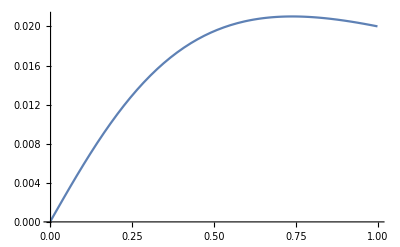

```mathematica
Plot[ψshoot[406/100,1/50][t],{t,ϵ,1-ϵ}]
```

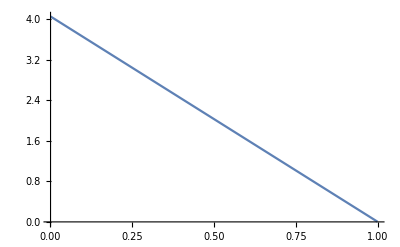

```mathematica
Plot[Abs[A0shoot[406/100,1/50][t]],{t,ϵ,1-ϵ}]
```

可以看到，A0的解几乎就是条直线，符合我们的预期（预期：相变点附近，ψ很小，ψ对eomA0几乎无贡献，所以A0’’=0,A0几乎是直线）

在画一个b0比较大的时候的场的解：

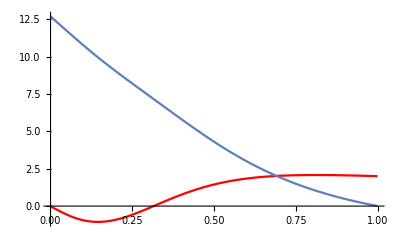

```mathematica
Show[Plot[ψshoot[4166/1000,2][t],{t,ϵ,1-ϵ},PlotStyle->Red],Plot[Abs[A0shoot[4166/1000,2][t]],{t,ϵ,1-ϵ}],PlotRange->All]
```

#### 2.4 用b0的值来表示a1（运用边界条件falloff[[3]] = d0 = ψ(1) ）

```mathematica
a1res[a1ini_,b0_]:=FindRoot[falloffres[a1,b0][[3]]==0,{a1,a1ini}]
```

注: a1ini是Findroot里寻找根的初始参数，是需要手动调整的，否则会找到明显错误的解

```mathematica
a1res[4,2]
```

{a1→4.16648}

```mathematica
data1=Join[Table[{a1res[4,b0],b0,falloffres[a1/.a1res[4,b0],b0]},{b0,1/1000,9/1000,1/1000}],
Table[{a1res[4,b0],b0,falloffres[a1/.a1res[4,b0],b0]},{b0,1/100,9/100,2/100}],
Table[{a1res[4,b0],b0,falloffres[a1/.a1res[4,b0],b0]},{b0,1/10,1,1/20}]]
```

{{{a1→4.06371},1/1000,{-4.063715306243162837,4.063716604728911,-1.93×10^-20,0.00294545201061377233}},{{a1→4.06371},1/500,{-4.063717183933453576,4.0637223778754175,-8.607×10^-20,0.00589090342014565653}},{{a1→4.06371},3/1000,{-4.063721363834579492,4.063733050214719,5.553×10^-19,0.0088363616817828461}},{{a1→4.0637},1/250,{-4.063726891538838785,4.0637476673435535,-5.172×10^-19,0.0117818298659470649}},{{a1→4.06369},1/200,{-4.0637342801607096,4.0637667424020535,5.639×10^-19,0.0147273094864386229}},{{a1→4.06368},3/500,{-4.063743249286660726,4.06378999499297,-1.3756×10^-18,0.0176728049378130587}},{{a1→4.06367},7/1000,{-4.063753927514921316,4.0638175537429599,3.604×10^-19,0.0206183190216902164}},{{a1→4.06365},1/125,{-4.063766279831097711,4.0638493836752481,3.0157×10^-18,0.0235638540388512216}},{{a1→4.06364},9/1000,{-4.06378018804233409,4.0638853666199651,-3.4949×10^-18,0.0265094141512658588}},{{a1→4.06362},1/100,{-4.063795786551511539,4.0639256370283361,-1.367×10^-18,0.0294550024255321774}},{{a1→4.06285},3/100,{-4.064453231736550784,4.0656220319769636,4.88×10^-18,0.0883773311341536816}},{{a1→4.0613},1/20,{-4.065768160826734832,4.0690156387802316,-1.098×10^-17,0.147336651443567351}},{{a1→4.05899},7/100,{-4.067740749989696883,4.0741081902892517,-2.271×10^-17,0.206357650696356037}},{{a1→4.0559},9/100,{-4.070371272075927272,4.080902295759466,3.8973×10^-17,0.265465059718968854}},{{a1→4.05407},1/10,{-4.071933347434621495,4.0849384640985442,-1.897×10^-17,0.295058908942141272}},{{a1→4.04204},3/20,{-4.082214128446528843,4.1115327118200656,3.075×10^-17,0.443553939876759272}},{{a1→4.02524},1/5,{-4.096618602564433289,4.148882760353816,-1.382×10^-17,0.593212007686621007}},{{a1→4.00369},1/4,{-4.115158022611413932,4.1971070037139651,3.127×10^-17,0.744428012640751608}},{{a1→3.97746},3/10,{-4.137846678790714906,4.256358074231725,-2.202×10^-17,0.897602987905875217}},{{a1→3.94661},7/20,{-4.164701708273924053,4.3268230676966535,2.058×10^-17,1.05314558345217983}},{{a1→3.91119},2/5,{-4.195742948384970758,4.4087238854257397,4.1914×10^-16,1.21147347961615362}},{{a1→3.8713},9/20,{-4.230992677692098187,4.5023175065719534,-1.875×10^-17,1.37301476064156892}},{{a1→3.82704},1/2,{-4.270475358432797572,4.607896301540285,1.179×10^-16,1.53820919311298511}},{{a1→3.7785},11/20,{-4.314217287628911628,4.725788246403003,2.98×10^-17,1.70750942027715648}},{{a1→3.72581},3/5,{-4.362246243483255031,4.8563571267037569,-2.435×10^-17,1.88138203129433025}},{{a1→3.66911},13/20,{-4.41459100324254153,5.000002527556762,-1.254×10^-16,2.0603084912380415}},{{a1→3.60853},7/10,{-4.471280886597457992,5.1571597854207486,-2.75×10^-18,2.24478589138591104}},{{a1→3.54423},3/4,{-4.532345165675367959,5.3282996373840606,-7.373×10^-17,2.43532749321660967}},{{a1→3.47639},4/5,{-4.597812420200669228,5.513927627775817,2.9928×10^-16,2.63246302661091754}},{{a1→3.4052},17/20,{-4.667709876825306176,5.7145833002144398,9.381×10^-17,2.83673876687875095}},{{a1→3.33084},9/10,{-4.742062600762808399,5.9308388689484804,-1.483×10^-16,3.04871720310767589}},{{a1→3.25353},19/20,{-4.820892689400718959,6.163297595309379,1.146×10^-16,3.2689764326960981}},{{a1→3.17349},1,{-4.904218374724920614,6.4125916387386995,-2.159×10^-16,3.49810912570619032}}}

```mathematica
data2 = Table[{a1res[2,b0],b0,falloffres[a1/.a1res[2,b0],b0]},{b0,11/10,2,1/10}]
```

{{{a1→3.0062},11/10,{-5.08440453192409583,6.9643423319635437,1.472×10^-16,3.98542946857937437}},{{a1→2.83097},6/5,{-5.2826535363736983,7.5916113611539773,4.9721×10^-16,4.51564556077155101}},{{a1→2.64999},13/10,{-5.498874437683741173,8.3001528725788988,-3.33×10^-17,5.09381933401021657}},{{a1→2.46552},7/5,{-5.732823740354240499,9.0957891812034883,-2.275×10^-16,5.72499734906928219}},{{a1→2.27988},3/2,{-5.98408183351957171,9.9842167317136681,-8.1808×10^-16,6.41407810408834722}},{{a1→2.09538},8/5,{-6.252038885115245525,10.970797204311361,3.377×10^-16,7.16566645207671353}},{{a1→1.9142},17/10,{-6.535893513533757432,12.060353167854058,-1.044×10^-16,7.98392962561501628}},{{a1→1.73836},9/5,{-6.834666173025318664,13.25699094689994,1.1562×10^-15,8.87247147691782738}},{{a1→1.56962},19/10,{-7.147227075226755302,14.563972130743651,-7.429×10^-16,9.83424067043098474}},{{a1→1.40944},2,{-7.472336038544633157,15.98364880620618,2.4638×10^-15,10.8714843208333907}}}

```mathematica
data3 = Table[{a1res[1/2,b0],b0,falloffres[a1/.a1res[1/2,b0],b0]},{b0,2,3,1/10}]
```

{{{a1→1.40944},2,{-7.472336038544633787,15.98364880620618,1.9897×10^-15,10.8714843208333904}},{{a1→1.25895},21/10,{-7.80868975658641269,17.517468080417886,-2.903×10^-16,11.9857512314233916}},{{a1→1.11892},11/5,{-8.154970891568897942,19.166040243156787,5.242×10^-16,13.1779413780672381}},{{a1→0.989805},23/10,{-8.509893650473666479,20.929256209811526,3.907×10^-16,14.4483911645515391}},{{a1→0.871746},12/5,{-8.872241624615643037,22.806434393295736,-7.73×10^-17,15.7969807037042803}},{{a1→0.764624},5/2,{-9.240895546987945909,24.796477046077124,3.×10^-17,17.2232483334851966}},{{a1→0.668111},13/5,{-9.614850354609718609,26.898018701714885,2.4962×10^-15,18.7265003071216385}},{{a1→0.581712},27/10,{-9.993222509256201903,29.109555319477363,-5.499×10^-16,20.3059067313516426}},{{a1→0.50482},14/5,{-10.37524935913509855,31.429547640740556,-4.181×10^-16,21.9605794736681293}},{{a1→0.43675},29/10,{-10.76028273182787668,33.85649776192914,-9.866×10^-16,23.689630627405089}},{{a1→0.376781},3,{-11.14777884041874642,36.389000583937835,-3.762×10^-16,25.4922131114791117}}}

```mathematica
data4 = Join[Table[{a1res[1/5,b0],b0,falloffres[a1/.a1res[1/5,b0],b0]},{b0,31/10,37/10,1/10}],
Table[{a1res[1/20,b0],b0,falloffres[a1/.a1res[1/20,b0],b0]},{b0,38/10,4,1/10}]]
```

{{{a1→0.324182},31/10,{-11.53728631629000579,39.025774543402824,4.28654×10^-14,27.3675459177419524}},{{a1→0.278233},16/5,{-11.92843369705542602,41.765675808593982,5.0695×10^-15,29.3149273960620342}},{{a1→0.238241},33/10,{-12.32091731633686839,44.607700681012887,4.385×10^-16,31.3337396851142305}},{{a1→0.203551},17/5,{-12.71449015987140834,47.55098002567194,-1.9584×10^-15,33.4234471555614064}},{{a1→0.173554},7/2,{-13.10895199565203897,50.594768996943287,-3.37621×10^-14,35.58359113310525}},{{a1→0.147691},18/5,{-13.50414085416375834,53.73843417573315,9.4296×10^-15,37.8137824846322486}},{{a1→0.125452},37/10,{-13.89992582980214959,56.981439940543167,-9.6714×10^-15,40.1136933026786562}},{{a1→0.106377},19/5,{-14.2962011012648416,60.323335053686523,-2.517×10^-16,42.4830487092399689}},{{a1→0.0900534},39/10,{-14.69288103074124845,63.763740275041827,-1.82×10^-14,44.9216190623690454}},{{a1→0.076116},4,{-15.08989617050414998,67.302336995969982,-8.07915×10^-14,47.429212686469145}}}

```mathematica
data5 = Table[{a1res[1/50,b0],b0,falloffres[a1/.a1res[1/50,b0],b0]},{b0,41/10,5,1/10}]
```

{{{a1→0.06424},41/10,{-15.4871900566160093,70.93885753216459,-3.71565×10^-14,50.0056697147003937}},{{a1→0.0541402},21/5,{-15.88471663230663925,74.67307659650974,-4.014×10^-16,52.6508566582245883}},{{a1→0.0455668},43/10,{-16.28243817907138135,78.50480406800949,-8.0191×10^-14,55.3646617997481347}},{{a1→0.0383015},22/5,{-16.68032369245887702,82.433879016229091,-4.3199×10^-15,58.1469912780023435}},{{a1→0.032155},9/2,{-17.07834758200831225,86.460164773786157,-1.11319×10^-13,60.9977660605470186}},{{a1→0.026963},23/5,{-17.47648859033085361,90.583544483809187,-6.21613×10^-14,63.9169190932314204}},{{a1→0.0225838},47/10,{-17.87472904280596327,94.803918172328842,-3.62×10^-16,66.9043933472655953}},{{a1→0.0188954},24/5,{-18.27305412422233744,99.121199540683736,2.6×10^-16,69.9601399317690514}},{{a1→0.0157929},49/10,{-18.67145137693298174,103.53531376581815,-7.52×10^-16,73.0841166015910428}},{{a1→0.0131866},5,{-19.06991027622285528,108.04619564342121,-1.341929×10^-12,76.276286750385331}}}

```mathematica
data6 = Join[Table[{a1res[1/200,b0],b0,falloffres[a1/.a1res[1/200,b0],b0]},{b0,51/10,58/10,1/10}],
Table[{a1res[1/500,b0],b0,falloffres[a1/.a1res[1/500,b0],b0]},{b0,59/10,6,1/10}]]
```

{{{a1→0.0109999},51/10,{-19.46842192985375095,112.65378848600892,-1.7236×10^-13,79.5366183732742765}},{{a1→0.00916731},26/5,{-19.86697872678358069,117.35804187739291,-5.77539×10^-14,82.8650832910875216}},{{a1→0.00763323},53/10,{-20.26557418911642683,122.15891159904666,-4.76514×10^-13,86.2616565489604689}},{{a1→0.00635042},27/5,{-20.66420275290695714,127.05635824775152,-1.0104×10^-13,89.7263158009591405}},{{a1→0.00527883},11/2,{-21.0628596433272966,132.0503467321917,-9.1295126×10^-12,93.2590413740475274}},{{a1→0.00438456},28/5,{-21.46154071874995014,137.14084567767516,-1.14974×10^-13,96.8598144509049351}},{{a1→0.00363899},57/10,{-21.86024241380098799,142.32782648189086,-3.4696×10^-14,100.528619193558951}},{{a1→0.00301795},29/5,{-22.25896163730368111,147.611263850305,-8.9036×10^-15,104.265440292321402}},{{a1→0.0025011},59/10,{-22.6576957010896547,152.9911346519497,-1.77835×10^-13,108.070263993130011}},{{a1→0.00207132},6,{-23.05644225218191561,158.46741772878693,-7.4847135×10^-12,111.943077362012175}}}

```mathematica
data7 = Join[Table[{a1res[1/1600,b0],b0,falloffres[a1/.a1res[1/1600,b0],b0]},{b0,61/10,69/10,1/10}],
{a1res[1/3000,7],7,falloffres[a1/.a1res[1/3000,7],7]}]
```

{{{a1→0.00171424},61/10,{-23.45519924516637982,164.04009386718227,-1.9074×10^-14,115.883868510438083}},{{a1→0.0014178},31/5,{-23.85396490261586707,169.7091456277449,-1.0948103×10^-11,119.892626160703841}},{{a1→0.00117188},63/10,{-24.2527376565179442,175.474556910793,-6.30855×10^-14,123.969339922872692}},{{a1→0.000968018},32/5,{-24.65151614432847842,181.33631293858759,-3.280615×10^-12,128.113999814911241}},{{a1→0.00079915},13/2,{-25.05029915673504919,187.29440008052071,-7.83355×10^-13,132.326596512960059}},{{a1→0.000659361},33/5,{-25.4490856589520189,193.34880586786554,-1.18872763×10^-10,136.607120911013138}},{{a1→0.00054372},67/10,{-25.84787469720744582,199.4995183749697,-1.396541×10^-12,140.955564607417104}},{{a1→0.000448118},34/5,{-26.24666548805874144,205.74652711226093,-4.32553×10^-13,145.371919365912042}},{{a1→0.000369132},69/10,{-26.6454573061169939,212.0898218401426,4.1898×10^-14,149.856177291078821}},{a1→0.000303912},7,{-27.0442495301953267,218.52939324468502,-3.541870422×10^-9,154.408330760038176}}

```mathematica
data8 = Join[Table[{a1res[1/5000,b0],b0,falloffres[a1/.a1res[1/5000,b0],b0]},{b0,71/10,75/10,1/10}],
Table[{a1res[1/20000,b0],b0,falloffres[a1/.a1res[1/20000,b0],b0]},{b0,76/10,8,1/10}]]
```

{{{a1→0.000250091},71/10,{-27.44304160594652353,225.06523271336971,-7.19815×10^-13,159.028372260021916}},{{a1→0.000205702},36/5,{-27.8418330807337166,231.6973322256799,-3.0966146×10^-11,163.716295256435904}},{{a1→0.000169112},73/10,{-28.2406234686723047,238.42568351233015,-2.6214669×10^-11,168.472091294153238}},{{a1→0.000138967},37/5,{-28.63941246603710495,245.25028014830551,-4.501213×10^-12,173.295755101863877}},{{a1→-0.000114144},15/2,{29.03819972797118193,-252.17111520856959,3.169386×10^-12,178.187279410858902}},{{a1→0.0000937153},38/5,{-29.43698495916624409,259.18818199379255,2.155555×10^-12,183.14665771218778}},{{a1→0.0000769099},77/10,{-29.83576793054213837,266.30147490558855,-8.456569×10^-12,188.173883515998412}},{{a1→0.0000630921},39/5,{-30.234548446266144,273.510988376001,1.1728357×10^-11,193.268950999537593}},{{a1→0.0000517361},79/10,{-30.63332627762756237,280.81671674419633,-1.62277405×10^-10,198.431852549464398}},{{a1→0.0000424074},8,{-31.0321013135856944,288.21865543328156,1.8788222×10^-11,203.662583538150964}}}

```mathematica
data9 = Join[Table[{a1res[1/40000,b0],b0,falloffres[a1/.a1res[1/40000,b0],b0]},{b0,81/10,85/10,1/10}],
Table[{a1res[1/200000,b0],b0,falloffres[a1/.a1res[1/200000,b0],b0]},{b0,86/10,9,1/10}]]
```

{{{a1→0.0000347475},81/10,{-31.43087338427478343,295.71679901884625,7.3477561×10^-11,208.961137184355964}},{{a1→0.00002846},41/5,{-31.8296424048873454,303.3111436599713,1.7838234×10^-11,214.327507730864505}},{{a1→0.0000233021},83/10,{-32.2284082678464036,311.00168468982121,7.432406×10^-12,219.761688871262401}},{{a1→0.0000190722},42/5,{-32.62717088128187234,318.78841789415806,1.591026×10^-11,225.263674858754156}},{{a1→0.0000156047},17/2,{-33.0259302065372232,326.67133989123726,1.0606181×10^-10,230.833459894026899}},{{a1→0.0000127632},43/5,{-33.42468615456680762,334.65044609945235,3.2769501×10^-11,236.471037938289948}},{{a1→0.0000104357},87/10,{-33.82343870681349658,342.72573361909156,8.78939422×10^-10,242.176403141852961}},{{a1→8.53024×10^-6},44/5,{-34.22218782036205401,350.89719855160877,1.502885212×10^-9,247.949549601941967}},{{a1→6.97016×10^-6},89/10,{-34.6209334905685243,359.16483818857843,2.991008874×10^-9,253.790471951423625}},{{a1→5.69365×10^-6},9,{-35.01967568686556613,367.52864889109639,2.92820395×10^-10,259.699163796964901}}}

#### 2.5 所有计算数据

因为全部重新算一遍要好几分钟，因此这里直接把之后可能会用到的所有数据全部保存下来

```mathematica
data = Join[data1,data2,data3,data4,data5,data6,data7,data8,data9];
```

```mathematica
data = {{{a1->4.0637135197052245},1/1000,{-4.06371530624316283664703714859011587466`19.373714283284233,4.06371660472891068852473889736433893071`16.917390865542643,-1.930962584242729179`3.8756757547290626*^-20,0.00294545201061377232584087383230075319`18.669399518583106}},{{a1->4.0637052849959785},3/1000,{-4.0637213638345794917480121134799403252`19.44246989729117,4.06373305021471901343547544144546662172`17.246142013019035,5.5532853480721990048`4.608899955496076*^-19,0.00883636168178284610097498108316126497`18.696058527738543}},{{a1->4.063689616739006},1/200,{-4.06373428016070960028950213022508555407`19.443042016906993,4.06376674240205347046803877343097291736`17.2501046021274,5.6386523992308584293`4.390366418015056*^-19,0.01472730948643862285570045371600216528`18.696276125440388}},{{a1->4.063666387264316},7/1000,{-4.06375392751492131594730544587165697275`19.42650504926336,4.06381755374295989002960376009120883249`17.147957200194934,3.6035116268784702149`4.133010438594454*^-19,0.02061831902169021637486980747266613229`18.689985637912216}},{{a1->4.063635478775989},9/1000,{-4.06378018804233408991338295281684319244`19.405003245445467,4.06388536661996508626591615117519834262`17.041514751641312,-3.49486524996312530532`5.0920583622908495*^-18,0.02650941415126585879889580582502111938`18.68172562756291}},{{a1->4.06361713323039},1/100,{-4.06379578655151153907384977249629616524`19.422872542641922,4.0639256370283361131907446969021317936`17.128279333256543,-1.36693414458828498676`4.572623934235822*^-18,0.0294550024255321774107065079705985936`18.688599173426674}},{{a1->4.0628453873255985},3/100,{-4.06445323173655078351844161337156319579`19.405788824318417,4.06562203197696357780511253053974331906`17.045148885958856,4.87970572706972733926`4.711479754811524*^-18,0.08837733113415368155103462519490606761`18.682030345562044}},{{a1->4.061302124464559},1/20,{-4.06576816082673483188587763100109361763`19.431951947624952,4.06901563878023156622996662792458667632`17.179474716413456,-1.097626200824657937012`4.737762789655372*^-17,0.14733665144356735068424525388152068192`18.692061365999177}},{{a1->4.058987901695178},7/100,{-4.06774074998969688309450620551843652001`19.427226381803685,4.07410819028925174734655735000376450511`17.152672976472136,-2.270539483557009177503`4.9288348642729805*^-17,0.20635765069635603740111969058929936555`18.690263109344126}},{{a1->4.05590356400226},9/100,{-4.07037127207592727206328989123326945951`19.409256644849155,4.08090229575946604431992328428065086911`17.061998418401117,3.897333533904460220032`5.124388033908562*^-17,0.26546505971896885360490739660620796687`18.683374394017857}},{{a1->4.054072922775188},1/10,{-4.07193334743462149536323021371572020092`19.42763829337711,4.08493846409854421275260467741426752564`17.155720448556032,-1.896983452045085269949`4.693614974553129*^-17,0.29505890894214127173107892792939234567`18.690422708857344}},{{a1->4.042042162629095},3/20,{-4.08221412844652884348419262220791128729`19.418578890474006,4.11153271182006557670529932076796480169`17.109228929614414,3.075257493663043541391`4.764158080410641*^-17,0.44355393987675927150715876956205747457`18.68696663637671}},{{a1->4.0252367308536945},1/5,{-4.09661860256443328922230894195476273884`19.43822781998615,4.14888276035381601449393503162568679889`17.223769878794382,-1.381981911236328042836`4.200971131311004*^-17,0.59321200768662100702501598179631081499`18.694469150069647}},{{a1->4.003694438771528},1/4,{-4.11515802261141393198335472198920265779`19.429506377021507,4.19710700371396511481591033873443884064`17.17390102507265,3.127406550854663204029`4.499986225280026*^-17,0.74442801264075160812970681882656828992`18.69116163293508}},{{a1->3.9774641658898666},3/10,{-4.13784667879071490556746141587612162407`19.387481529000343,4.25635807423172478862131640907706886982`16.981113273152104,-2.201927197770947091855`4.413771352440251*^-17,0.89760298790587521705003236594738253967`18.67490607533979}},{{a1->3.9466059886116795},7/20,{-4.16470170827392405316015322327928853115`19.423514001417843,4.32682306769665352207111921413327558045`17.14906437146009,2.057602161427505496522`4.193476810862727*^-17,1.05314558345217983309684889738204025029`18.68890338167526}},{{a1->3.9111914339683977},2/5,{-4.19574294838497075804667356403612754879`19.434881268782284,4.40872388542573970726128515832661243491`17.21971989980336,4.1914121863438359059172`5.388993293443653*^-16,1.21147347961615361740825357459574640387`18.69326211258686}},{{a1->3.8713036831865093},9/20,{-4.23099267769209818712526205732398399722`19.39107360785089,4.5023175065719534018948630891691877839`17.01038410690458,-1.874811709696569798719`4.1490828507227935*^-17,1.3730147606415689170292766990294601318`18.6763619284684}},{{a1->3.82703784013901},1/2,{-4.27047535843279757185264920769625654244`19.380381402992654,4.6078963015402845727457352582236896954`16.975280005541997,1.1793280678494032863563`4.926854666447838*^-16,1.53820919311298510826353633529411232205`18.672144346948023}},{{a1->3.7785011713315453},11/20,{-4.31421728762891162763980613464205681627`19.378974374802162,4.72578824640300348909738209334671606523`16.97674614185182,2.980236328911364113643`4.287534345296256*^-17,1.70750942027715648364460760635311911192`18.671600387680826}},{{a1->3.725813387589582},3/5,{-4.36224624348325503077267261507501105074`19.404824741300384,4.85635712670375693034515131309228647123`17.088807244066228,-2.43469829844762707875`4.083189107144846*^-17,1.88138203129433024787013552480327751886`18.681799929584383}},{{a1->3.6691068530830386},13/20,{-4.41459100324254152966116997107604013939`19.42124788615766,5.00000252755676200409077432059705931369`17.176375331493247,-1.2536484398121823579379`4.694512050095808*^-16,2.06030849123804149851058630794111547666`18.688174310417146}},{{a1->3.608526843716551},7/10,{-4.47128088659745799229900397299397445144`19.415911999898654,5.15715978542074861119699731796362232884`17.15724811299785,-2.74866448275131452736`3.0190769511343674*^-18,2.24478589138591103991698755552170868425`18.686148246338046}},{{a1->3.5442317060371247},3/4,{-4.53234516567536795893575147650407371904`19.38546194170586,5.32829963738406056323247599635095003641`17.03263023343551,-7.373407632462229328734`4.509369483491322*^-17,2.43532749321660967128475280108113256551`18.674266800018867}},{{a1->3.4763929719091258},4/5,{-4.59781242020066922845043591143048269581`19.377493702398947,5.51392762777581699989185630571436210265`17.01146697544954,2.9928484711099963528584`5.104295910362527*^-16,2.6324630266109175436268626404607124874`18.67111480260758}},{{a1->3.405195410700259},17/20,{-4.66770987682530617556817147745660712958`19.40402544184741,5.71458330021443980010021972173796472074`17.127975963246726,9.380610430069222794885`4.491910007007847*^-17,2.83673876687875094506596381463486488224`18.681627442332836}},{{a1->3.3308369621841694},9/10,{-4.74206260076280839941594258735493061085`19.41017142885269,5.93083886894848042942515519327940895708`17.166008160760054,-1.4826557034853173467144`4.637873839648003*^-16,3.04871720310767589173617984853736803591`18.68405545622154}},{{a1->3.253528565478709},19/20,{-4.82089268940071895867069554759826735721`19.36047312100997,6.16329759530937929307227924954360422706`16.980454600141275,1.1456255241119680073165`4.631527601285427*^-16,3.26897643269609809758482468887383723938`18.664305106767095}},{{a1->3.1734938320736514},1,{-4.90421837472492061396651105931567501638`19.38394049483128,6.41259163873869951902477954414378178214`17.07415068446688,-2.1589679385556503367556`4.821644784953347*^-16,3.49810912570619032324919398655231662239`18.673802079708192}},{{a1->3.006200092818928},11/10,{-5.08440453192409582984677762506649938329`19.404295521653133,6.96434233196354371849986900745105535229`17.17990413918879,1.4718656574743538255888`4.537173229687053*^-16,3.98542946857937436813848546687494296481`18.681912877991742}},{{a1->2.830974989436518},6/5,{-5.28265353637369830005551958166601499842`19.401608665643717,7.59161136115397730998277802247569373362`17.189554582735944,4.972060797777942058108`5.019692718913421*^-16,4.51564556077155101160037752139786721973`18.68093964501976}},{{a1->2.6499889188921797},13/10,{-5.49887443768374117349862965861889417993`19.346521061961322,8.3001528725788988054911670188837133925`17.009115669264627,-3.325161259097895371797`3.9282519963395326*^-17,5.09381933401021656510974695154175815851`18.65874701493755}},{{a1->2.4655176594885586},7/5,{-5.73282374035424049901106590256434661871`19.403564158489157,9.09578918120348831337497237701234581306`17.24335409277791,-2.2747876729837971091994`4.5686676208586405*^-16,5.72499734906928218575589757709719947144`18.68188898544621}},{{a1->2.2798826441589406},3/2,{-5.98408183351957171031544452433658529123`19.385492642537177,9.98421673171366810327185111510919505511`17.18938527699265,-8.1807673459175220510772`5.1296528202449565*^-16,6.4140781040883472227776239583574801612`18.67479848409672}},{{a1->2.0953798178927525},8/5,{-6.2520388851152455247576042726046118949`19.354625915694722,10.97079720431136122127017530120923420553`17.101540375531226,3.3768458712535816770317`4.769811164244729*^-16,7.16566645207671352542283886768457702215`18.66231405653281}},{{a1->1.9142019895322633},17/10,{-6.53589351353375743174924852789887719907`19.315812379107633,12.06035316785405753306068853146004141647`17.008855612409715,-1.0443401023586884640166`4.279633195742657*^-16,7.98392962561501628127220195577287282637`18.645956490790244}},{{a1->1.7383615653964744},9/5,{-6.83466617302531866379508413110159118063`19.261821315931066,13.25699094689993891072407066073661780324`16.89797170234193,1.15618786728513991515121`5.341241078730944*^-15,8.87247147691782737553399204758188536509`18.62187869911115}},{{a1->1.5696215910909037},19/10,{-7.14722707522675530236179293594499793605`19.37379335420015,14.56397213074365132063191714386067068487`17.23469432633037,-7.4288625628607694209549`4.929961515998588*^-16,9.83424067043098474453064177742804409602`18.670430941538612}},{{a1->1.4094423523617585},2,{-7.47233603854463315656467684823800360717`19.270975888507333,15.98364880620618328620144616955388238118`16.961719385829223,2.4637878115339146813028`5.572372698599616*^-15,10.87148432083339071558375012577516048422`18.62618899196064}},{{a1->1.4094423523617587},2,{-7.47233603854463378726899920917008414797`19.270975888507127,15.98364880620618301847840535090966515628`16.96171938582875,1.9896783988807037879193`5.479552281195544*^-15,10.87148432083339040141662313017008549729`18.626188991960543}},{{a1->1.2589487927815743},21/10,{-7.80868975658641269019230114333085596138`19.334538961300794,17.5174680804178863860159722434193116693`17.148235838123863,-2.9025717616085512557`4.516238420019052*^-16,11.98575123142339164513666201202172659686`18.654266112199515}},{{a1->1.1189208047542454},11/5,{-8.1549708915688979415936842268652652169`19.319197099909616,19.16604024315678727811070699079947453702`17.124892553889225,5.2416065293221674993249`4.756197743172845*^-16,13.17794137806723810532710041827512934007`18.64775851549427}},{{a1->0.989805229657168},23/10,{-8.50989365047366647903688992623119320817`19.266921787105304,20.92925620981152608391282101981794790676`17.01360120692134,3.9074659518501503516477`4.652734761538145*^-16,14.44839116455153912010566494802976069972`18.624500050587915}},{{a1->0.8717456278258238},12/5,{-8.87224162461564303662532593523447307666`19.265152622025614,22.80643439329573638224696261822362183954`17.02895483928065,-7.731159217114556352251`3.9119123450101787*^-17,15.79698070370428025228787435770952981889`18.623742638862307}},{{a1->0.764624342470718},5/2,{-9.24089554698794590909561514316548550021`19.30473282330745,24.79647704607712357130287854071772976268`17.144528963512744,2.996369831821067147325`3.4169022866492043*^-17,17.22324833348519661625707435462950676735`18.64164903802792}},{{a1->0.6681110292234348},13/5,{-9.61485035460971860923220134753683410922`19.266966505119655,26.89801870171488463967626037907988368032`17.070290427025625,2.49621094532910139550994`5.34496809016477*^-15,18.72650030712163852958879317495432460372`18.62469356215972}},{{a1->0.5817124637194401},27/10,{-9.99322250925620190344488732005341633762`19.280755151740472,29.10955531947736270861446332600148840087`17.120530913842074,-5.4985602718782659563027`4.638071349233543*^-16,20.30590673135164259471091959036720185852`18.631055088607493}},{{a1->0.5048196625718051},14/5,{-10.37524935913509855439487064149835115864`19.27144815493115,31.42954764074055582291428120595345074298`17.11569737186237,-4.1810656156556439501995`4.494904656445792*^-16,21.96057947366812931059719852793323689793`18.62687022646761}},{{a1->0.43674975077420347},29/10,{-10.76028273182787668096103550660510741419`19.29873416827507,33.85649776192914003552680533527085990451`17.19938230374983,-9.8658926044819661257399`4.802901128863901*^-16,23.6896306274050889640340436209178958484`18.639260845852085}},{{a1->0.37678124424689796},3,{-11.14777884041874641522794510527445824861`19.217796360902653,36.38900058393783461270490953406817905385`17.032310895256163,-3.7617674187070379831017`4.4289237391505125*^-16,25.49221311147911174876602501799791105887`18.60159602007031}},{{a1->0.3241824195942355},31/10,{-11.53728631629000578993176747693295616464`19.2094791378672,39.02577454340282411140976287550707181893`17.03130147389554,4.286538658513433702254509`6.460048652027612*^-14,27.36754591774195240236648569559409073882`18.59756719586223}},{{a1->0.2782330991720727},16/5,{-11.92843369705542602424231870692751400378`19.23958635451467,41.76567580859398204224184153119163087316`17.108263125311556,5.06950686963435291802628`5.481692187659714*^-15,29.31492739606203420977177031233695035706`18.61219616256887}},{{a1->0.238240570238299},33/10,{-12.3209173163368683887967005888701404162`19.2763548442088,44.60770068101288715994287058957553355383`17.20594680286124,4.3852452274381736411694`4.355102151914985*^-16,31.33373968511423045364864886988200769153`18.629412424498266}},{{a1->0.2035505299374674},17/5,{-12.71449015987140833903729870117249631641`19.15654859287033,47.55098002567193611358572808964028349864`16.976193275353474,-1.95836911466125240191923`5.058570632374959*^-15,33.4234471555614064020512251514061170984`18.57084878908123}},{{a1->0.1735539848284422},7/2,{-13.10895199565203897345144927718664525439`19.217861131317033,50.59476899694328650482164117238646043617`17.105892590618513,-3.376208857658566410580514`6.2366333129680696*^-14,35.58359113310525003737270342539779691152`18.601861489535718}},{{a1->0.1476909628774718},18/5,{-13.50414085416375833612842139789629153238`19.14516257861714,53.73843417573315133607934488963694564978`16.983289727016622,9.42959867233537228100128`5.691417352142444*^-15,37.81378248463224858417497572390155742485`18.564940787515386}},{{a1->0.1254517775493713},37/10,{-13.89992582980214959284281363672265438633`19.179602651045897,56.9814399405431669835464853288327961827`17.058193152500674,-9.67138865040458525532559`5.663164827516319*^-15,40.11369330267865623416171917434538150707`18.582854159405723}},{{a1->0.10637654782768291},19/5,{-14.29620110126484159689435066680049517957`19.198598678354095,60.32333505368652310545288829026092732482`17.106883710159053,-2.5170195264019076608107`4.043758324367107*^-16,42.48304870923996888135727625145262307148`18.592478157464633}},{{a1->0.09005341862722521},39/10,{-14.69288103074124844792635987593878864073`19.221316471985293,63.76374027504182723035649406448408623076`17.164425545097686,-1.820023070336668318145088`5.864348790440485*^-14,44.92161906236904535175452255859581083387`18.603728961409306}},{{a1->0.07611595191439306},4,{-15.08989617050414997857601070373352125532`19.178570668693887,67.30233699596998247553394547187893924411`17.093197160613965,-8.079147505127097331643454`6.512610608696661*^-14,47.42921268646914497687112519881836234618`18.58244347534713}},{{a1->0.06423999028706605},41/10,{-15.48719005661600929931135298386229314313`19.168590771691974,70.93885753216459013213341364823001788621`17.086502833174116,-3.715648813106923143307886`6.156696836655007*^-14,50.00566971470039367940045152953819528227`18.57735674762006}},{{a1->0.05414024430183272},21/5,{-15.8847166323066392499083073990870391001`19.106177669551368,74.6730765965097360754525218900492593283`16.99026869628265,-4.0135148222187534522403`4.186330618399588*^-16,52.65085665822458831343943837725160442283`18.544093293337887}},{{a1->0.04556677801039584},43/10,{-16.28243817907138134739097887873127223692`19.098317471381257,78.5048040680094868272546940080599028344`16.98852059228567,-8.01909571132058050295422`6.466433204716679*^-14,55.36466179974813470160826033080574504886`18.53977470479252}},{{a1->0.03830154367092852},22/5,{-16.68032369245887702479988603831732140956`19.21364194967253,82.43387901622909118620105949883663828905`17.205992340483924,-4.31993211158397027236514`5.132398437525754*^-15,58.14699127800234346169060282485555602303`18.6001858687482}},{{a1->0.03215501378452463},9/2,{-17.07834758200831225086666070649575918716`19.191108571968485,86.46016477378615695785568787887767173134`17.172379190525326,-1.1131855234622440438959458`6.535981379881946*^-13,60.99776606054701860708172715694340739806`18.58899593548721}},{{a1->0.026963023333671562},23/5,{-17.47648859033085361438205554560877320579`19.15836020596588,90.58354448380918677311386931466029196623`17.122153313201753,-6.216128826407149561358036`6.277476554471655*^-14,63.91691909323142039722334580156319464249`18.572216563859477}},{{a1->0.022583823130870186},47/10,{-17.87472904280596326555785059610450688635`19.148645577423874,94.80391817232884244188237067561580568177`17.11499168197313,-3.6201349725515389908722`4.026313085759595*^-16,66.904393347265595259483553435893842635`18.56714692151466}},{{a1->0.018895374815926395},24/5,{-18.27305412422233744489351148222468259209`19.11387101480537,99.12119954068373620398975277441767438338`17.06546134064218,2.5991680318994237060568`3.8725599692760637*^-16,69.96013993176905141187575272040484562039`18.548484610481832}},{{a1->0.015792889774712066},49/10,{-18.67145137693298174149654535079777242926`19.12965520755443,103.53531376581814785714751117901733567614`17.101604903314,-7.520207921681413348638`4.311171462685519*^-16,73.08411660159104280756012395714074150236`18.557080830298542}},{{a1->0.013186626413812415},5,{-19.06991027622285527722509101668885757692`19.093317452508504,108.0461956434212113896586224745593115261`17.050894566066905,-1.34192863676631495145864041`7.551537807498277*^-12,76.27628675038533095676499511307622388531`18.537172497446992}},{{a1->0.01099989323590544},51/10,{-19.4684219298537509500500510761529510707`19.213620161758257,112.65378848600891991873778394302101340441`17.275431905261726,-1.7236035760305091348158283`6.59671366089338*^-13,79.5366183732742764626913556744768157695`18.60045457295904}},{{a1->0.00916730597377861},26/5,{-19.86697872678358069305361559239022148341`19.199428525642272,117.35804187739290567669351969110875655801`17.25629954911204,-5.775389731509129732575972`6.112809401125892*^-14,82.86508329108752160290948800666657956395`18.593436151851137}},{{a1->0.007633231461924859},53/10,{-20.265574189116426834301188209573516258`19.21057558800643,122.15891159904665829963025108966745208977`17.287317891936127,-4.7651397340034886109888445`7.0049208733177775*^-13,86.26165654896046885545260344091163467424`18.599025152861486}},{{a1->0.0063504228294695925},27/5,{-20.6642027529069571392606859304162184138`19.063134401662854,127.05635824775152421281067231073016718912`17.038999228843434,-1.0103955637752358255213439`6.360731172628385*^-13,89.72631580095914046765116071008639618028`18.520145058782962}},{{a1->0.0052788313045057204},11/2,{-21.06285964332729659980307341696933284141`18.868443713221247,132.05034673219173303183844871464476553286`16.775053751413004,-9.12951262104382105435358679`8.267815578917675*^-12,93.25904137404752738279682393852455172891`18.39793474266718}},{{a1->0.004384564591830754},28/5,{-21.46154071874995014435506030868565477346`19.075507741243516,137.14084567767515948788247728378147454406`17.075099086060114,-1.149740941043312686447955`6.382687101148896*^-13,96.85981445090493510761602531141532749259`18.527267438660108}},{{a1->0.0036389886281175624},57/10,{-21.86024241380098799321233548760457210773`19.22099724105517,142.3278264818908584222537091475873740559`17.34261977958016,-3.469584606443717393172532`5.793176446216925*^-14,100.5286191935589505058183414228003388878`18.604308935086678}},{{a1->0.0030179486756862486},29/5,{-22.25896163730368110722922744836684372039`19.119154907468232,147.61126385030499519773187739078225573298`17.162142347128434,-8.90357285075341487700397`5.232602782729953*^-15,104.26544029232140166468812483298520308462`18.551627969403544}},{{a1->0.0025010970028392344},59/10,{-22.6576957010896546792940286385259330734`18.922258071172337,152.99113465194971923659277266333777714384`16.87801199041558,-1.7783538063480305976742852`6.509655332702861*^-13,108.07026399313001148316064787428250535632`18.433748847980482}},{{a1->0.0020713208418640483},6,{-23.05644225218191561023573268940756521264`19.122389464769096,158.46741772878693421394102562664984491854`17.183244650255737,-7.48471349779529127906828885`8.125530862153827*^-12,111.94307736201217542365286240490549729879`18.553436922768622}},{{a1->0.0017142410868516212},61/10,{-23.45519924516637981908308917117380789581`19.060350255436646,164.04009386718226952303916177893237102786`17.09091573097851,-1.907392246727251850272337`5.525677421450981*^-14,115.88386851043808326398828559626961712965`18.518674262379076}},{{a1->0.0014177955788773752},31/5,{-23.85396490261586706816113585418935067973`19.10607849971017,169.70914562774490237257425031697835400039`17.17118292886588,-1.094810331082381530834449435`8.264414170436327*^-11,119.89262616070384085712246824156657341069`18.544540356494338}},{{a1->0.0011718750201931852},63/10,{-24.25273765651794424947276677377861111265`18.959411878761202,175.47455691079295269415873254795995518265`16.958666761222933,-6.308550909342834309566211`6.008254408952397*^-14,123.96933992287269165430604257530502766318`18.457629740088155}},{{a1->0.0009680179230901562},32/5,{-24.65151614432847841531528160866042357398`19.011146310317894,181.33631293858758746713811406607537533294`17.039262732837578,-3.28061498340874594333079825`7.716878488359143*^-12,128.11399981491124066680855672240326007231`18.489633488191632}},{{a1->0.0007991499427315713},13/2,{-25.05029915673504918636158598902197507751`19.04297632175994,187.29440008052070630775370725818297294921`17.093553580619027,-7.833550268989437754742885`7.08200716971527*^-13,132.32659651296005895673746444629445187504`18.50861916387899}},{{a1->0.0006593608397115733},33/5,{-25.44908565895201889275995901787161495104`18.996869951687884,193.34880586786554409746389662380715283759`17.032710550001767,-1.1887276336017729401143363624`9.246819302256572*^-10,136.60712091101313803840274535207377030725`18.480971431313975}},{{a1->0.0005437203861615555},67/10,{-25.84787469720744582418813201378883730407`19.068462524870473,199.49951837496970139395994471132144530908`17.1465545162716,-1.39654080811774784124515285`7.3046864699372875*^-12,140.95556460741710436490002802677725597996`18.5234478341831}},{{a1->0.000448118300386054},34/5,{-26.24666548805874144146993752870993391655`19.098377342504982,205.74652711226093120326570304359780533324`17.201018593423925,-4.3255338591009443700496782`6.778693846050449*^-13,145.37191936591204194978618969945734518134`18.540385638203933}},{{a1->0.0003691317901606711},69/10,{-26.64545730611699394604260647107980061817`18.93492316922703,212.08982184014263385226642467391222568657`16.966692567315413,4.189758941165852134455549`5.743041197251276*^-14,149.85617729107882051956042315167822942272`18.44204057518548}},{a1->0.0003039121727458092},7,{-27.04424953019532667522769742440300411087`18.972427234905513,218.52939324468501596797024826145666865846`17.0249177017428,-3.54187042204681504902547467333`10.664501156295104*^-9,154.40833076003817645453041878809356125024`18.46588163158501},{{a1->0.0002500913557253153},71/10,{-27.4430416059465235348804548754643431937`19.016969140559237,225.06523271336970743447159798611150772429`17.095210607409925,-7.1981499232806084594706421`6.964670105610877*^-13,159.02837226002191588738525529497677675173`18.493232538648368}},{{a1->0.0002057024352568057},36/5,{-27.84183308073371656997330276454770872753`18.81359868484953,231.69733222567987289845246283778889745593`16.828763499935583,-3.0966146046421000622233656`8.532934366285781*^-11,163.71629525643590382450451136105204327637`18.36003741398354}},{{a1->0.00016911165761959715},73/10,{-28.24062346867230472313200437350038374206`18.9634537675462,238.42568351233014672857714165266882493774`17.031502119093606,-2.621466908146565061138302955`8.494452583027657*^-11,168.4720912941532380265863823608322229224`18.4602696083801}},{{a1->0.00013896678030330596},37/5,{-28.63941246603710495420246369495486632205`19.015421980245364,245.25028014830551441369666433690362076903`17.111800426486706,-4.50121345408767313282918614`7.723369504864378*^-12,173.2957551018638773718576546861848761858`18.492333050245662}},{{a1->-0.00011414448954495562},15/2,{29.03819972797118192692434792683722931649`19.05985225091861,-252.17111520856959310672463508955883912326`17.184722831101375,3.16938648097455347392531344`7.559288647863524*^-12,178.18727941085890218707088088982308679089`18.518603714209508}},{{a1->0.00009371526631725248},38/5,{-29.43698495916624408651633952675927732036`19.005048135069874,259.18818199379255415250446262778073470031`17.108820390526695,2.15555499054000426560432646`7.3787967617801105*^-12,183.14665771218778012569416483655471652856`18.48606774129394}},{{a1->0.00007690990220431801},77/10,{-29.83576793054213836794439213477885489157`19.031345679441653,266.30147490558854846379291658754273517654`17.153426824263327,-8.45656867839271741351970706`7.962172517220917*^-12,188.17388351599841204190444668055194728517`18.501899027840203}},{{a1->0.00006309213423444577},39/5,{-30.23454844626614403841027622276778918134`18.83744286850691,273.51098837600103071063466329145363693825`16.894988017440472,1.172835720320365776701445937`8.048964893647184*^-11,193.26895099953759302822045642635029536722`18.376732202330437}},{{a1->0.00005173609998311975},79/10,{-30.63332627762756236898245914116332843766`19.058271082092787,280.81671674419633368616948588443695994551`17.20594405139584,-1.6227740454449493073823497719`9.221886459483548*^-10,198.43185254946439796226801418335245564981`18.517736994442245}},{{a1->0.00004240741737142848},8,{-31.03210131358569439844321685447302040541`19.03005977010386,288.21865543328156282650124861730767823987`17.168881479262243,1.878822179928411231509749452`8.274472467006044*^-11,203.66258353815096372223841306679231004831`18.501163582583654}},{{a1->0.000034747534571864786},81/10,{-31.43087338427478342910112168994474131981`19.068355065962383,295.71679901884624781032878950138598562311`17.23298733480999,7.347756121799522577970580149`8.854686910944546*^-11,208.96113718435596405416061916672386283228`18.523584271302177}},{{a1->0.00002845999111048462},41/5,{-31.82964240488734536140385708576263440457`18.86097122946307,303.31114365997128843870877842116718716364`16.947582919890774,1.783823371275616091242202209`8.194978958723876*^-11,214.32750773086450452611321816380059907502`18.392940654308774}},{{a1->0.00002330210222839197},83/10,{-32.22840826784640360856798405649515450854`18.956431929458414,311.00168468982121190863206305446853391278`17.080016767362633,7.43240633623198737749207239`7.830371287507585*^-12,219.76168887126240138446319068523365026245`18.455882867307015}},{{a1->0.000019072195373042756},42/5,{-32.62717088128187233792055217591960623783`19.00777518654976,318.7884178941580563885770462586642574447`17.158202217477257,1.591025974778334688290735371`8.157263791620924*^-11,225.2636748587541556758421221458830031929`18.487788801235688}},{{a1->0.000015604683507200307},17/2,{-33.02593020653722319503616739472690584266`19.005193224819248,326.67133989123725587633717454962108951511`17.159811889249234,1.0606181064657575700575464077`8.970321846359406*^-10,230.83345989402689917201852653137385058595`18.486224222129692}},{{a1->0.000012763237153224543},43/5,{-33.42468615456680761583741905492688892467`19.00332638903906,334.650446099452346122977015904845523053`17.162401411469332,3.276950073646456650242934349`8.449588268174733*^-11,236.47103793828994796196423864404970564617`18.48509196147251}},{{a1->0.000010435714503304123},87/10,{-33.82343870681349657852916627979781858197`19.02408714884956,342.72573361909155992165897457450315768761`17.198045611060678,8.7893942157008796859001015988`9.869107307462803*^-10,242.17640314185296118711829221974278014791`18.497652259176114}},{{a1->8.530238663519757*^-6},44/5,{-34.22218782036205400572624242331475798452`19.014422535424487,350.89719855160876665264406471032004420466`17.188973367808032,1.50288521173362260947036228972`10.091327440823104*^-9,247.94954960194196733604921274440191585629`18.491842368864518}},{{a1->6.970158327238181*^-6},89/10,{-34.62093349056852425595485928823678123094`18.931932909351445,359.16483818857842991104808420831536328092`17.078043766150568,2.99100887406126849422717723682`10.367308001892814*^-9,253.79047195142362531624430553993040818842`18.44018318574528}},{{a1->5.693649613481037*^-6},9,{-35.01967568686556613355536301810691869475`19.01070567445647,367.52864889109638817927005676807135483104`17.19369939848186,2.9282039523729157287973863493`9.36063867442639*^-10,259.69916379696490099901234496833624083199`18.489602600620003}}};
```

#### 2.6 利用2.4求出的数据画序参量与温度的关系

```mathematica
ptdata1 =Table[{(3/(4π))/Abs[data1[[i]][[3]][[1]]] ,Abs[data1[[i]][[3]][[4]]]},{i,1,Length[data1]}];
```

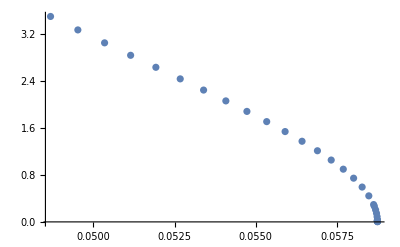

```mathematica
ListPlot[ptdata1,PlotRange->All]
```

画图：注意T = τ/(4π/3) = 3/4π 横轴是T/μ

```mathematica
ptdata2 =Table[{(3/(4π))/Abs[data1[[i]][[3]][[1]]] ,Sqrt[Abs[data1[[i]][[3]][[4]]]]},{i,1,Length[data1]}];
```

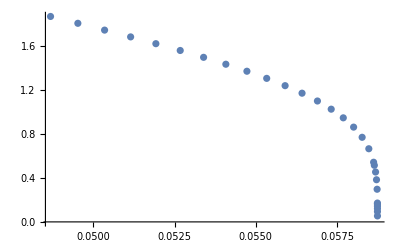

```mathematica
ListPlot[ptdata2]
```

```mathematica
{a1res[4,b0],b0,falloffres[a1/.a1res[4,b0],b0]}/.{b0->1/10000}
```

{{a1→4.06382},1/100000,{-4.063818451144627475,4.0638184512744712,2.8397×10^-20,0.0000294548434232653014}}

求相变温度Tc

```mathematica
Tc = (3/(4π))/Abs[data[[1]][[3]][[1]]]
```

0.05874732766615660079

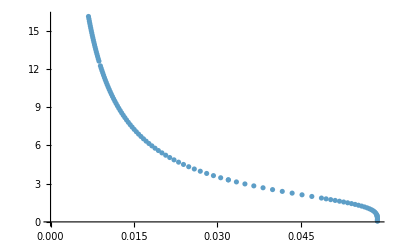

```mathematica
ListPlot[Table[{(3/(4π))/Abs[data[[i]][[3]][[1]]] ,Sqrt[Abs[data[[i]][[3]][[4]]]]},{i,1,Length[data]}]]
```

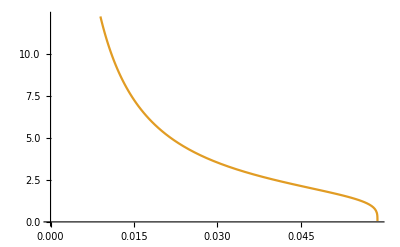

```mathematica
ListLinePlot[Table[{(3/(4π))/Abs[data[[i]][[3]][[1]]] ,Sqrt[Abs[data[[i]][[3]][[4]]]]},{i,1,Length[data]-20}]]
```

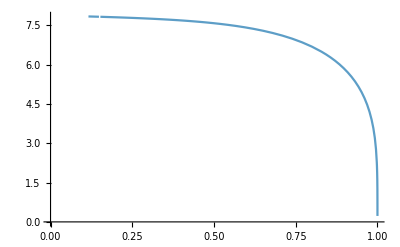

```mathematica
ListLinePlot[Table[{(3/(4π)/0.058747327)/Abs[data[[i]][[3]][[1]]] ,Sqrt[Abs[data[[i]][[3]][[4]]]]/Abs[data[[i]][[3]][[1]]]/0.058747327},{i,1,Length[data]}]]
```

```mathematica
{(3/(4π)/0.058747327)/Abs[data[[112]][[3]][[1]]] ,Sqrt[Abs[data[[112]][[3]][[4]]]]/Abs[data[[112]][[3]][[1]]]/0.058747327}
```

{0.116041,7.83312}

```mathematica
dataf1 = Table[{Log[1-(3/(4π)/0.0587473276661566007873756403866531726)/Abs[data1[[i]][[3]][[2]]]],Log[Abs[data1[[i]][[3]][[4]]]]},{i,5,15}]
```

{{-11.27727946503,-4.218051720558492509},{-10.9042971166,-4.035728265134485507},{-10.5902370312,-3.881575325457903558},{-10.31922372201,-3.748041349585166004},{-10.08149652915,-3.630255358085488775},{-9.868978511164,-3.524891521661445904},{-7.664934536162,-2.426139777357658457},{-6.64338682995779,-1.91503516471595937},{-5.9712858070952,-1.57814444716188521},{-5.46992071975331,-1.32627204877221517},{-5.25996900614754,-1.22058025124868434}}

```mathematica
Fit[dataf1,{1,x},x]
```

1.3992773433+0.49863118289 x

### 3. Conductivity

```mathematica
eomAx[ω_]=1/h[u] D[h[u]*Ax'[u],u]+((ω/(τ*h[u]))^2-(2 ψ[u]^2)/h[u])*Ax[u]
```

Ax[u] (ω^2/((1-u^3)^2)-(2 ψ[u]^2)/(1-u^3))+(-3 u^2 Ax'[u]+(1-u^3) Ax''[u])/(1-u^3)

We need to impose the incoming wave boundary condition: Ax ~ (1-u)* exp(Iω/3) (u->1)

```mathematica
Axhor[u_] = (1-u)^(I*ω/3)*(1+e0*(1-u)+e1*(1-u)^2+e2*(1-u)^3);
```

```mathematica
eomAxseries = Series[Simplify[eomAx[ω]/(1-u)^(I*ω/3) /.{ψ[u]->ψh[a1,b0,u],Ax->Axhor}],{u,1,3}];
```

我们用(u-1)的0,1,2次幂项来用a0,b1表示e0,e1,e2

```mathematica
eomAxsol = Solve[Table[SeriesCoefficient[eomAxseries,n]==0,{n,0,2}],{e0,e1,e2}];
```

带回Axhor表达式，我们就得到了在u=1邻域内Ax的解，再把该解当成边界条件条件，使用NDSolve积分即可得到完整解

```mathematica
Axh[ω_,a1_,b0_,u_] = Evaluate[Axhor[u] /.eomAxsol];
```

```mathematica
Axshoot[ω_,a1_,b0_] := Ax/.NDSolve[{eomAx[ω]==0 /.{ψ[u]->ψshoot[a1,b0][u]},Ax[1-ϵ]==Axh[ω,a1,b0,1-ϵ],Ax'[1-ϵ]==D[Axh[ω,a1,b0,u],u]/.{u->1-ϵ}},Ax,{u,1-ϵ,ϵ}][[1]];
```

```mathematica
σ[ω_,a1_,b0_]:= (I*Axshoot[ω,a1,b0]'[ϵ])/(ω*Axshoot[ω,a1,b0][ϵ])
```

```mathematica
Axshoot[1,406/100,1/10][ϵ]
```

{0.891742+0.461381 ⅈ}

```mathematica
Axshoot[1,406/100,1/10]'[ϵ]
```

{0.444507-0.878918 ⅈ}

```mathematica
σ[1,1,0]
```

{0.990743-0.00632908 ⅈ}

```mathematica
σimdata = Table[{ω,Abs[Im[σ[ω,4055/100,1/50]]][[1]]},{ω,1/1000,1/50,1/1000}]
```

{{1/1000,0.608013},{1/500,0.30396},{3/1000,0.202625},{1/250,0.151955},{1/200,0.121546},{3/500,0.101272},{7/1000,0.0867736},{1/125,0.0759049},{9/1000,0.0674552},{1/100,0.0606842},{11/1000,0.0551466},{3/250,0.0505289},{13/1000,0.0466157},{7/500,0.043266},{3/200,0.0403597},{2/125,0.0378201},{17/1000,0.0355674},{9/500,0.0335688},{19/1000,0.0317812},{1/50,0.0301685}}

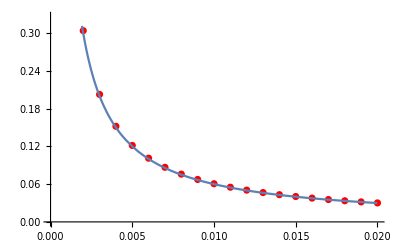

```mathematica
plot3=ListPlot[σimdata,PlotStyle->Red];
plot4=Plot[0.0006/x,{x,1/1500,1/50}];
Show[plot3,plot4]
```

绘制一组T=4.06/4.904 Tc 的数据

{{0.1,0.157922},{0.2,0.160973},{0.3,0.16614},{0.4,0.173549},{0.5,0.183367},{0.5,0.183367},{1.,0.276478},{1.5,0.456266},{2.,0.694805},{2.5,0.886519},{3.,0.98634},{3.5,1.01723},{4.,1.02332},{4.5,1.01721},{5,1.01479},{6,1.00761},{7,1.0035},{8,1.00119},{9,1.00009},{10,0.999908},{10,0.999908},{12,1.00091},{14,1.00116},{16,0.999832},{18,0.999032},{20,1.00001}}

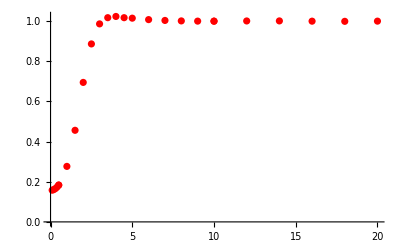

```mathematica
σredata = Join[Table[{ω,Abs[Re[σ[ω,3.173,1]]][[1]]},{ω,0.1,0.5,0.2}],
Table[{ω,Abs[Re[σ[ω,3.173,1]]][[1]]},{ω,1,4.5,0.5}],
Table[{ω,Abs[Re[σ[ω,3.173,1]]][[1]]},{ω,5,10,1}],
Table[{ω,Abs[Re[σ[ω,3.173,1]]][[1]]},{ω,10,20,2}]]
Show[ListPlot[σredata,PlotStyle->Red]]
```

```mathematica
dd = {data1[[1]],data2[[1]],data2[[9]],data3[[9]],data6[[4]]}
```

{{{a1→4.06371},1/1000,{-4.063715306243162837,4.063716604728911,-1.93×10^-20,0.00294545201061377233}},{{a1→3.0062},11/10,{-5.08440453192409583,6.9643423319635437,1.472×10^-16,3.98542946857937437}},{{a1→1.56962},19/10,{-7.147227075226755302,14.563972130743651,-7.429×10^-16,9.83424067043098474}},{{a1→0.50482},14/5,{-10.37524935913509855,31.429547640740556,-4.181×10^-16,21.9605794736681293}},{{a1→0.00635042},27/5,{-20.66420275290695714,127.05635824775152,-1.0104×10^-13,89.7263158009591405}}}

这组数据对应的T/Tc分别是：

```mathematica
Table[(3/(4π)/0.058747327)/Abs[dd[[i]][[3]][[1]]],{i,1,5}]
```

{1.,0.799251,0.568572,0.391674,0.196655}

```mathematica
σdata = Table[Table[{ω,σ[ω,a1/.dd[[i]][[1]],dd[[i]][[2]]]},{ω,0.5,20,0.125}],{i,1,5}];
```

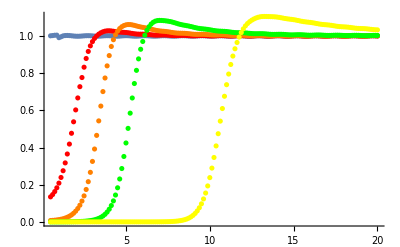

```mathematica
Show[ListPlot[Table[{σdata[[1]][[i]][[1]],Re[σdata[[1]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}]],
ListPlot[Table[{σdata[[2]][[i]][[1]],Re[σdata[[2]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Red],
ListPlot[Table[{σdata[[3]][[i]][[1]],Re[σdata[[3]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Orange],
ListPlot[Table[{σdata[[4]][[i]][[1]],Re[σdata[[4]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Green],
ListPlot[Table[{σdata[[5]][[i]][[1]],Re[σdata[[5]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Yellow],
PlotRange->All]
```

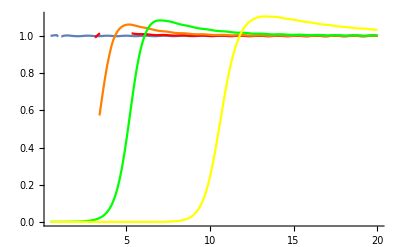

```mathematica
Show[ListLinePlot[Table[{σdata[[1]][[i]][[1]],Re[σdata[[1]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}]],
ListLinePlot[Table[{σdata[[2]][[i]][[1]],Re[σdata[[2]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Red],
ListLinePlot[Table[{σdata[[3]][[i]][[1]],Re[σdata[[3]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Orange],
ListLinePlot[Table[{σdata[[4]][[i]][[1]],Re[σdata[[4]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Green],
ListLinePlot[Table[{σdata[[5]][[i]][[1]],Re[σdata[[5]][[i]][[2]][[1]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Yellow],
PlotRange->All]
```

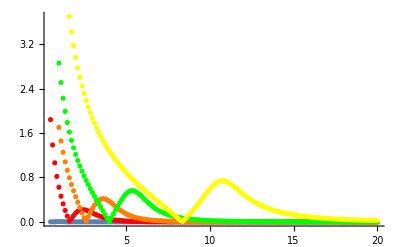

```mathematica
Show[ListPlot[Table[{σdata[[1]][[i]][[1]],Abs[Im[σdata[[1]][[i]][[2]][[1]]]]},{i,1,Length[σdata[[1]]]}]],
ListPlot[Table[{σdata[[2]][[i]][[1]],Abs[Im[σdata[[2]][[i]][[2]][[1]]]]},{i,1,Length[σdata[[1]]]}],PlotStyle->Red],
ListPlot[Table[{σdata[[3]][[i]][[1]],Abs[Im[σdata[[3]][[i]][[2]][[1]]]]},{i,5,Length[σdata[[1]]]}],PlotStyle->Orange],
ListPlot[Table[{σdata[[4]][[i]][[1]],Abs[Im[σdata[[4]][[i]][[2]][[1]]]]},{i,5,Length[σdata[[1]]]}],PlotStyle->Green],
ListPlot[Table[{σdata[[5]][[i]][[1]],Abs[Im[σdata[[5]][[i]][[2]][[1]]]]},{i,10,Length[σdata[[1]]]}],PlotStyle->Yellow],
PlotRange->All]
```

```mathematica
Length[data]
```

112

```mathematica
data[[1]][[3]]
```

{-4.063715306243162837,4.063716604728911,-1.93×10^-20,0.00294545201061377233}

```mathematica
nndata = Table[{(3/(4π))/Abs[data[[i]][[3]][[1]]],Abs[Sqrt[data[[i]][[3]][[4]]]],σ[0.0001,a1/.data[[i]][[1]],data[[i]][[2]]]},{i,70,89,1}]
```

{{0.01251880114693063608,8.73362964353225428,{1.0688×10^-8-56854.3 ⅈ}},{0.01226254575219371102,8.91833047006412947,{6.89601×10^-9-58080.5 ⅈ}},{0.01201654352787910023,9.10302605132422554,{4.44832×10^-9-59306.7 ⅈ}},{0.01178019494587296802,9.28771535680117992,{2.86877×10^-9-60533.1 ⅈ}},{0.01155294581128996546,9.47239757405479368,{1.84968×10^-9-61759.5 ⅈ}},{0.0113342831258657375,9.65707209116963812,{1.19236×10^-9-62986. ⅈ}},{0.01112373141175617435,9.84173838561587325,{7.68477×10^-10-64212.7 ⅈ}},{0.01092084937206023354,10.0263961219153391,{4.95172×10^-10-65439.4 ⅈ}},{0.01072522692333287276,10.2110450147044892,{3.19009×10^-10-66666.3 ⅈ}},{0.0105364825173445098,10.3956848736930272,{2.05482×10^-10-67893.3 ⅈ}},{0.01035426073227975494,10.5803155606065066,{1.3233×10^-10-69120.4 ⅈ}},{0.01017823008632257524,10.7649369951912902,{8.52047×10^-11-70347.8 ⅈ}},{0.01000808107216017552,10.9495491304758225,{5.48521×10^-11-71575.2 ⅈ}},{0.00984352438965518025,11.134151962447463,{3.53086×10^-11-72802.8 ⅈ}},{0.009684289324848186248,11.3187455053513435,{2.27232×10^-11-74030.6 ⅈ}},{0.009530122300901031803,11.5033298011036813,{1.4623×10^-11-75258.6 ⅈ}},{0.00938078553536818461,11.6879048982703969,{9.40403×10^-12-76486.7 ⅈ}},{0.009236055862791504093,11.87247087203911,{6.05382×10^-12-77715.1 ⅈ}},{0.009095723597592135691,12.0570277998316004,{3.88845×10^-12-78943.6 ⅈ}},{0.00895959156921796333,12.2415757683020049,{2.50822×10^-12-80172.3 ⅈ}}}

```mathematica
a = Table[Log[Re[nndata[[i]][[3]]][[1]]],{i,1,Length[nndata]}]
b= Table[nndata[[i]][[2]],{i,1,Length[nndata]}]
```

```mathematica
c= Table[{b[[i]],a[[i]]},{i,1,Length[a]}]
```

{{8.73362964353225428,-18.3541},{8.91833047006412947,-18.7923},{9.10302605132422554,-19.2307},{9.28771535680117992,-19.6694},{9.47239757405479368,-20.1083},{9.65707209116963812,-20.5473},{9.84173838561587325,-20.9866},{10.0263961219153391,-21.4261},{10.2110450147044892,-21.8658},{10.3956848736930272,-22.3057},{10.5803155606065066,-22.7457},{10.7649369951912902,-23.186},{10.9495491304758225,-23.6264},{11.134151962447463,-24.0669},{11.3187455053513435,-24.5076},{11.5033298011036813,-24.9484},{11.6879048982703969,-25.3899},{11.87247087203911,-25.8303},{12.0570277998316004,-26.273},{12.2415757683020049,-26.7114}}

```mathematica
Fit[c,{1,x},x]
```

2.46422-2.38303 x

```mathematica
2.38/(4π/3)
```

0.568183

```mathematica
2*0.568*7.83
```

8.89488